```mathematica
SetDirectory[NotebookDirectory[]];
```

## Panels

```mathematica
xMin=0.5;
xMax=4.2;
yMin=0;
yMax=0.2;
xMax2=xMax-xMin;
dx=0.1;
dy=0.5;
dy2=0.15;
dy3=0.22;
cfMAX[x_]:=ColorData["SunsetColors"][(x-0.1)/0.45];
barMAX=Graphics[{
{Raster[{Range[0.1,0.55,1/1000]},{{xMin,yMin},{xMax,yMax}},ColorFunction->cfMAX]},AbsoluteThickness[cm[0.02]],Line[{{xMin,yMin},{xMax,yMin},{xMax,yMax},{xMin,yMax},{xMin,yMin}}],
Line[{{xMin+0/3*xMax2,0},{xMin+0/3*xMax2,-dy2}}],
Line[{{xMin+1/3*xMax2,0},{xMin+1/3*xMax2,-dy2}}],
Line[{{xMin+2/3*xMax2,0},{xMin+2/3*xMax2,-dy2}}],
Line[{{xMin+3/3*xMax2,0},{xMin+3/3*xMax2,-dy2}}],
Line[{{xMin+1*xMax2,0},{xMin+1*xMax2,-dy2}}],
Inset[Style["0.1",FontFamily->"Helvetica",FontSize->7],{xMin+0/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.25",FontFamily->"Helvetica",FontSize->7],{xMin+1/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.4",FontFamily->"Helvetica",FontSize->7],{xMin+2/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.55",FontFamily->"Helvetica",FontSize->7],{xMin+3/3*xMax2,-dy3},{Center,Top}]




},PlotRange->{{0,xMax+xMin},{yMin-2*dy,yMax+dy}},ImageSize->cm[xMax+xMin],ImagePadding->0]
```

-Graphics-

```mathematica
fixNum[num_]:=(
If[StringCount[num,"e"]==1,ToExpression[StringTake[num,{1,-5}]]*10^-5.,ToExpression[num]]
)
fixNumList[numIN_]:=(
numOUT={};Do[AppendTo[numOUT,fixNum[numIN[[ii]]]],{ii,1,Length[numIN]}];numOUT

)
ffmMAX[pi_,pt_,pr_,pd_]:=(
maxIN=Import["FFM//output//max//max_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_.dat","Table"];
max={};Do[AppendTo[max,maxIN[[ii]][[1]]],{ii,1,Length[maxIN]}];
{pt,Log[fixNum[pr]/fixNum[pi]],Mean[max]}
)
minMax[v_,x0_,x1_,y0_,y1_]:=(
{Min[Max[v[[1]],x0],x1],Min[Max[v[[2]],y0],y1]})
isSame[v1_,v2_]:=Total[Total[Abs[v1-v2]]]<0.0001
count2[xyz_,x_]:=(
cn=0;Do[If[isSame[xyz[[ii]],x],cn+=1],{ii,1,Length[xyz]}];
cn)
trueLines[linesIN_]:=(
linesOUT={};
Do[
If[count2[linesIN,linesIN[[jj]]]==1,AppendTo[linesOUT,linesIN[[jj]]]],{jj,1,Length[linesIN]}];
linesOUT)
```

```mathematica
plotMax[piForPlot_]:=(
ptList={0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1};
prList={
"1",

"0.88914",
"8.8914e-05",
"0.088914",
"0.0088914",
"0.00088914",

"1.58114e-05",
"0.158114",
"0.0158114",
"0.00158114",
"0.000158114",

"2.81171e-05",
"0.281171",
"0.0281171",
"0.00281171",
"0.000281171",

"5e-05",
"0.5",
"0.05",
"0.005",
"0.0005"
};
giniOutList={};

linesExperiment={};

(*x distance between points*)
dx=0.05;

(*y distance between points*)
dy0=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[2]]-Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]];
dy1=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]]-Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-2]];

size=3*6/5;

(*smallest and largest values in x,y direction*)
xMIN=0;
xMAX=1;
yMIN=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]];
yMAX=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]];

Do[
Do[
GG=ffmMAX[piForPlot,ptList[[i]],prList[[j]],0.026];
AppendTo[giniOutList,GG];
AppendTo[giniAllList,GG[[3]]];

If[Abs[GG[[3]]-0.36]<0.06,

x0=GG[[1]];
y0=GG[[2]];

(*if p_r == 1, dy is smaller*)
If[prList[[j]]=="1",dy=dy1,dy=dy0];

(*if p_r == 1, dy is smaller*)
If[prList[[j]]=="0.88914",dyUP=dy1,dyUP=dy0];

(*add four lines surrounding the coordinate if withing standard deviation of experiment*)
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0-dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX]
}];

];

,{j,1,Length[prList]}],{i,1,Length[ptList]}];



b=ListDensityPlot[giniOutList,ColorFunction->cfMAX,ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{{0,1},{yMIN,yMAX},{0.1,0.55}}];


(*Lines around experimentally comparable values*)
lineColor=Cyan;
lineTh=0.03;

linesplot=ListLinePlot[trueLines[linesExperiment],PlotRange->{
{0,1},{Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]],Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]]}},PlotStyle->{{lineColor,AbsoluteThickness[cm[lineTh]]}},AspectRatio->1];
fLegend=5;
FigC=plotBack[
{b,linesplot},
xTicks->{0,0.25,0.5,0.75,1},
yTicks->{Log[0.000001],Log[0.00001],Log[0.0001],Log[0.001],Log[0.01],Log[0.1],Log[1],Log[10],Log[100],Log[1000],Log[10000]},
yReplace->{Row[{Superscript[Style["10"],Style["-6",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-5",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-4",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-3",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-2",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-1",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["0",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["1",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["2",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["3",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["4",FontSize->fLegend]]}]},
tickLength->0.12,
plotRange->{{0,1},{yMIN,yMAX}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.2,0.6,1.2,1.2},
plotLabels->{
Row[{
Style["Coupling "],Subscript[Style["p",Italic],Style["t",FontSize->fLegend]]}],
Row[{Style["Ratio "],Subscript[Style["p",Italic],Style["r",FontSize->fLegend]],Style["/"],Subscript[Style["p",Italic],Style["i",FontSize->fLegend]]}]},
labelsDistance->{0.55,0.8},
plotTitle->True,
titleText->Row[{Subscript[Style["p",Italic],Style["i",FontSize->fLegend]],
Style[" = "],Style[piForPlot]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
```

```mathematica
piList={"1","0.1","0.01","0.001","0.0001","1e-05"};
panels={};
giniAllList={};
Do[AppendTo[panels,plotMax[piList[[iT]]]];Print[piList[[iT]]],{iT,1,Length[piList]}]
```

1

0.1

0.01

0.001

0.0001

1e-05

```mathematica
Max[giniAllList]
```

0.539021

```mathematica
Min[giniAllList]
```

0.104815

## Figure

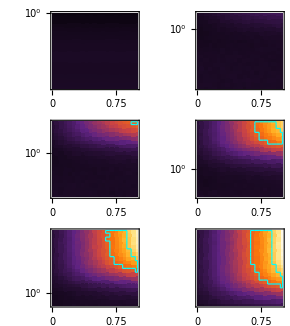

```mathematica
tMAX=Row[{Style["Largest cluster fractional size",FontFamily->"Arial",FontSize->7]}];
dX=5;
dY=-5;
dY2=-1.2;

FigED5=figure[10.25,16.8,
elements->Join[{tMAX},{barMAX},panels],
elementCoordinates->{
{0.5*dX+1.2+3*6/5/2,-0.6},
{0.5*dX+1.2+3*6/5/2,-1.3},

{0*dX,0*dY+dY2-0.5},
{1*dX,0*dY+dY2-0.5},
{0*dX,1*dY+dY2-0.5},
{1*dX,1*dY+dY2-0.5},
{0*dX,2*dY+dY2-0.5},
{1*dX,2*dY+dY2-0.5}
},
centeredElements->{1,2}]
```

```mathematica
Export["figs//SYS_ED_Fig5.pdf",FigED5]
```

figs//SYS_ED_Fig5.pdf